{σ→0.402217}

FindFit::nrgnum: The gradient is not a vector of real numbers at {α, p} = {0.44, 2.8}.

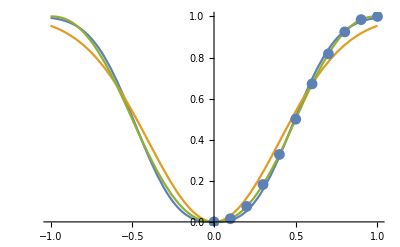

```mathematica
y[x_]:=If[x≤0.5,1/2(2x)^η,1-1/2(2(1-x))^η];
a[x_]:=1-d(2 x^3-3 x^2+1);
Gauss[x_]:=1-Exp[-x^2/(2 σ^2)];
GeneralizedGaussian[x_]:=1-Exp[-Abs[x]^p/(2 α^p)];
xy=Table[{x,a[y[Abs[x]]]/.{d->1,η->1.19}},{x,0,1,0.1}];
fit=FindFit[xy,Gauss[x],{{σ,-1}},x]
fit2=FindFit[xy,GeneralizedGaussian[x],{{α,0.44},{p,2.8}},x,Method->QuasiNewton];
Show[Plot[{GeneralizedGaussian[x]/.fit2,Gauss[x]/.fit,a[y[Abs[x]]]/.{d->1,η->1.19}},{x,-1,1},PlotRange->All],ListPlot[xy]]
```

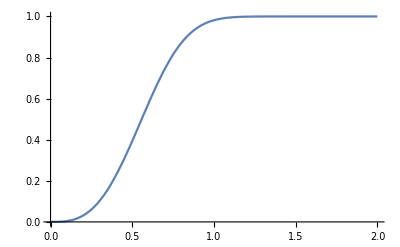

```mathematica
Plot[GeneralizedGaussian[x]/.{α->0.5,p->3},{x,0,2}]
```

```mathematica
GeneralizedGaussian[x]/.{α->1,p->2}
```

1-ⅇ^(-1/2 Abs[x]^2)

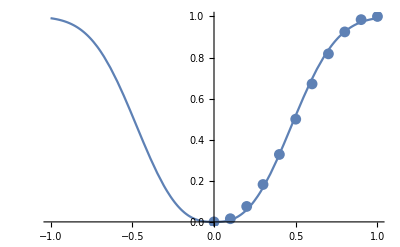

```mathematica
Show[Plot[GeneralizedGaussian[x]/.{α->0.435,p->2.71},{x,-1,1},PlotRange->All],ListPlot[xy]]
```